## Sources

The main paper I am following: arXiv:2410.04262v1 [hep-th] 5 Oct 2024
Logarithm Approximations:
	>This website
	>This presentation

## Code

#### Package Loading

```mathematica
<<NCAlgebra`
```

------------------------------------------------------------

NCAlgebra - Version 6.0.3

Compatible with Mathematica Version 10 and above



Authors:



  J. William Helton*

  Mauricio de Oliveira&



* Math, UCSD, La Jolla, CA

& MAE, UCSD, La Jolla, CA



with major earlier contributions by:



  Mark Stankus$ 

  Robert L. Miller#



$ Math, Cal Poly San Luis Obispo

# General Atomics Corp



Copyright: 

  Helton and de Oliveira 2023

  Helton and de Oliveira 2017

  Helton 2002

  Helton and Miller June 1991

  All rights reserved.



The program was written by the authors and by:

  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,

  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,

  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 

  The beginnings of the program come from eran@slac.

  Considerable recent help came from Igor Klep.



Current primary support is from the 

  NSF Division of Mathematical Sciences.

  

This program was written with support from 

  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,

  UCSD Faculty Mentor Program,

  and US Department of Education.



For NCAlgebra updates see:



  www.github.com/NCAlgebra/NC

  www.math.ucsd.edu/~ncalg



------------------------------------------------------------

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

## Functions

### NC Variable Handling

This section contains functions and auxiliary objects for handling non commuting variables

#### generateOperatorSet

Takes a length and a list of operators and produces all words of length up to the given length.

```mathematica
generateOperatorSet[operatorLength_,operators_]:=Flatten[DeleteDuplicates@Flatten[{1,Table[NonCommutativeMultiply@@word,{n,1,operatorLength},{word,Tuples[operators,n]}]},1]]
```

#### commutationPNXM

Takes the powers of x and p of a pair like p^m**x^n and passes p to the other side so that all operator pairs have p to the right.

```mathematica
commutationPNXM[m_,n_]:=If[
m==1,(*Checks if there is only one power of p*)
x^(n-1)*(-I)*n+x^(n)**p (*If there is only one power it just passes p to the right of the powers of x*),
commutationPNXM[m-1,n-1] *(-I)*n+commutationPNXM[m-1,n]**p(*If there are more than one powers of p then it passes them all to the right recursively*)
]
```

#### commutationRules

Not a function. Here are declared the rules governing the non commutative variables x and p.

```mathematica
commuationRules={
p**x->-I+x**p,
aj[x]->x,
aj[p]->p
};
```

#### NCProductList

Splits an expression containing operators into a list containing only the operator products.

```mathematica
NCProductList[expr_]:=Module[{terms},
terms=If[Head[expr]===Plus,List@@expr,{expr}];(*Checks of the Head of the expresion is summation e.i. expr of the form expr1+expr2. If it is then it splits it and adds each term into a list. If it is not then wraps the expression in a list*)

terms=terms/. (c_?NumericQ f_:>f)/. (c_?NumericQ*f_:>f);(*Gets rid of any numerical multiplicative factors*)

terms=DeleteCases[terms,_?NumericQ];(*Deletes cases where a number is left on its own*)

terms]
```

#### getSymbols

Takes a operator expression and breaks it into a list containing the operators. e.g: p**x**x**p->{p,x,x,p}

```mathematica
getSymbols[expression_]:=DeleteDuplicates@Cases[expression,_Symbol,Infinity]
```

### String Variable Handling

#### compress

Takes a word list and replaces adjoint occurrences of  a letter into the letter concatenated with the number of occurrences, i.e. “PPP”  "P3" or “PXXPP”"PX2P2".

```mathematica
compress[word_List]:=StringJoin[Map[If[Length[#]==1,First[#],First[#]<>ToString[Length[#]]]&,Split[word]]]
```

#### generateWords

Takes a character list and a word length and returns all possible words up to the given length after compressing them using compress.

```mathematica
generateWords[chars_List,L_Integer]:=DeleteDuplicates@(compress/@Flatten[Table[Tuples[chars,n],{n,1,L}],1])
```

#### expectationValue

Takes an expression containing operator products and returns the same expression but with commuting variables where each combination of operators becomes its own commuting variables effectively turning it into an expectation value

```mathematica
expectationValue[operator_]:=Module[
{commutingVar,productList=NCProductList[operator],replacementRule},
If[Length[productList]==0,
productList=List[productList]];
replacementRule=MapThread[#1->#2&,{productList,ToExpression[StringReplace[ToString[productList,InputForm],{"**"->"","^"->"","x"->"X","p"->"P"}]]}];
operator/.replacementRule
]
```

#### countWordLength

Counts and returns the length of a commuting variable word

```mathematica
countWordLength[commutingWord_]:=Total[ToExpression[Flatten[Characters[StringReplace[ToString[commutingWord],{RegularExpression["([a-zA-Z])(?=\\d)"]->"",RegularExpression["[a-zA-Z]"]->"1"}]]]]]
```

### Relations Handling

This section contains the functions that implement the commutator relation constrains such as the Schwinger-Dyson Equation  and the canonical commutation relations  as well as their corresponding axillary functions.

#### produceSwingerDyson

Takes a list of operator words and a Hamiltonian and returns a list of equations including the expectation values of operators using expectationValue. It implements the equation  for some operator O

```mathematica
produceSwingerDyson[operatorWordList_,H_]:=Module[
{internalList={},expectationValueList},
Do[
internalList=DeleteDuplicates[DeleteCases[Join[internalList,{NCExpandReplaceRepeated[operator**H-H**operator,commuationRules]}],0]]
,{operator,operatorWordList}];
expectationValueList=Table[Thread[expectationValue[item]==0],{item,internalList}];
expectationValueList
]
```

#### produceCannonical

Produces the relations that come from the canonical commutation relations. Employs:

```mathematica
produceCannonical[operatorList_]:=Module[
{preList=Flatten[Table[
expectationValue[NCExpand[I*operator1**operator2]]==expectationValue[NCExpandReplaceRepeated[operator1**(x**p-p**x)**operator2,commuationRules]]
,{operator1,operatorList},{operator2,operatorList}],1],finalList},
preList
]
```

#### solveRelations

```mathematica
solveRelations[relationList_]:=Module[
{solved={},independentVariables={},notSolved=relationList,solutions={},backup=0,symbols,troubleshoot=False,solution,independent,dependent},
While[Length[notSolved]!=0,
If[backup==4*Length[relationList],
Print["Oops"];
Break[]];
If[troubleshoot,
Print["=========="];
Print["Not Solved"];
Print[notSolved];
Print["Length"];
Print[Length[notSolved]];
Print["Solved"];
Print[solved];
Print["Solutions"];
Print[solutions];
Print["Independent Variables"];
Print[independentVariables];
Print["=========="]
];
Do[
If[troubleshoot,Print["---InDo---"];];
symbols=getSymbols[relations];
If[troubleshoot,Print["Got Symbols"];
Print[symbols]];
If[Length[symbols]==1,
solution=Flatten[Solve[relations]];
solved=Join[solved,{relations}];
solutions=DeleteDuplicates[Join[solutions,solution]];
If[troubleshoot,
Print["++++++++++"];
Print["Current Length is 1"];
Print["Symbols"];
Print[symbols];
Print["Relation"];
Print[relations];
Print["Solution"];
Print[solution];
Print["++++++++++"]
];
];
If[Length[symbols]==2,
independent={First[MinimalBy[symbols,countWordLength]]};
independentVariables=DeleteDuplicates[Join[independentVariables,independent]];
dependent=Complement[symbols,independentVariables];
solved=Join[solved,{relations}];
solutions=DeleteDuplicates[Join[solutions,Flatten[Solve[relations,dependent]]]];
If[troubleshoot,
Print["++++++++++"];
Print["Current Length is 2"];
Print["Symbols"];
Print[symbols];
Print["Relation"];
Print[relations];
Print["Solution"];
Print[solution];
Print["Independent Variable"];
Print[independent];
Print["Dependent"];
Print[dependent];
Print["++++++++++"]
];
];
If[Length[symbols]>2,
dependent={First[MaximalBy[symbols,countWordLength]]};
independent=Complement[symbols,dependent];
independentVariables=DeleteDuplicates[Join[independentVariables,independent]];
solved=Join[solved,{relations}];
solutions=DeleteDuplicates[Join[solutions,Flatten[Solve[relations,dependent]]]];
If[troubleshoot,
Print["++++++++++"];
Print["Current Length is greater than 2"];
Print["Symbols"];
Print[symbols];
Print["Relation"];
Print[relations];
Print["Solution"];
Print[solution];
Print["Independent Variable"];
Print[independent];
Print["Dependent"];
Print[dependent];
Print["++++++++++"]
];
];
ClearAll[independent,solution];
,{relations,notSolved}];
If[troubleshoot,Print["---OutDo---"]];
notSolved=Complement[notSolved,solved];
notSolved=notSolved/.solutions;
backup=backup+1;
];
{solutions,independentVariables}
]
```

#### finalSearchSpace

Crosschecks between a matrix and a list of variables and returns a list containing the list of variables extended to include any variable in the matrix that is not included in the original list.

```mathematica
finalSearchSpace[matrix_,independent_]:=Module[
{additions,fullList},
additions=Complement[Cases[matrix,_Symbol,∞],independent];
fullList=Join[independent,additions];
fullList
]
```

#### asignDomains

Takes a list and assigns each element a domain based on if the corresponding operetator is hermitean or not. Basically, if the word only contains P or X then it is real and is complex otherwise. The "domains" are boolean-responses to the question if the opperator is hermetian or not. It is done this way to make it easier to use with CVXPY.

```mathematica
asignDomains[list_]:=Module[
{returnList,
real=Table[If[Xor[StringContainsQ[ToString[item],"X"],StringContainsQ[ToString[item],"P"]],item],{item,list}],
realRules
},
returnList=Association[Table[If[Xor[StringContainsQ[ToString[item],"X"],StringContainsQ[ToString[item],"P"]],ToString[item]->False,ToString[item]->True],{item,list}]];

returnList
]
```

#### returnCoefficients

Takes a matrix and returns a dictionary with keys "constant" and the variables of the matrix as strings and with values 2 item lists containing the real and imaginary part of the corresponding coefficient matrices. I.e. breaks down a matrix M into: M=a0+a1X1+a2X2+a3X3+...-> <|"constant"->{Re[a0],Im[a0]},"X1"->{Re[a1],Im[a1]},...|>. The splitting between real and imaginary is done so that it can be used with python's imaginary unit instead.

```mathematica
returnCoefficients[matrix_]:=Module[
{output=<||>,variables=Variables[matrix],indeces=ToString[#]&/@Variables[matrix]},
output["constant"]=Module[{m=matrix/.Thread[variables->0]},
{Re[m],Im[m]}
];
Do[
output[indeces[[i]]]=Module[
{m=Table[Coefficient[matrix[[l,j]],variables[[i]]],{l,1,Length[matrix]},{j,1,Length[matrix]}]},
{Re[m],Im[m]}]
,{i,1,Length[variables]}];
output
]
```

### Matrix Builders

All the following functions take as input an operator word list() and return different types of expectation value matrices

#### generateODaggerOMatrix

Returns a matrix of the form

```mathematica
generateODaggerOMatrix[operatorBasis_]:=Table[
expectationValue[NCExpandReplaceRepeated[aj[operatori]**operatorj,commuationRules]],
{operatori,operatorBasis},{operatorj,operatorBasis}]
```

#### generateOODaggerMatrix

Returns a matrix of the form

```mathematica
generateOODaggerMatrix[operatorBasis_]:=Table[
expectationValue[NCExpandReplaceRepeated[operatorj**aj[operatori],commuationRules]],
{operatori,operatorBasis},{operatorj,operatorBasis}]
```

#### generateODaggerCommutatorHOMatrix

Takes an extra parameter, the Hamiltonian, and returns a matrix of the form

```mathematica
generateODaggerCommutatorHOMatrix[operatorBasis_,H_]:=Table[
expectationValue[NCExpandReplaceRepeated[aj[operatori]**(H**operatorj-operatorj**H),commuationRules]],
{operatori,operatorBasis},{operatorj,operatorBasis}]
```

### Semidefinite Relaxation of the Matrix Logarithm: Functions

For the Gauss-Radau Quadrature I am following this source.
More about this approximation and the matrix logarithm in SDPs here [mathematica is not behaving with the copy paste].

#### getAbscissas

Takes as argument an integer and returns a list with the proper abscissas for the quadrature rule in ascending order. The abscissas are the roots of the equation:  where  are the Legendre Polynomials. Some notes on the values: The function returns the abscissas  .

```mathematica
getAbscissas[m_]:=Table[items[[2]],{items,Flatten[NSolve[(LegendreP[m-1,x]+LegendreP[m,x])/(1+x)==0,x]]}]
```

#### getWeight

Returns the quadrature weight with the formula: where $x_j$ is the corresponding abscissa valid for all non-endpoint abscissas.

```mathematica
getWeight[m_,x_]:=(1-x)/(m*LegendreP[m-1,x])^2
```

#### getQuadrature

Returns the full list of abscissas pairs after shifting them into the [0,1] interval with the transformation: . The endpoint weight is given by  and the (before transformation) corresponding abscissa is -1.

```mathematica
getQuadrature[m_]:=Module[
{abscissas=getAbscissas[m],pairs},
pairs=Table[{x,getWeight[m,x]},{x,abscissas}];
{(#[[1]]+1)/2,#[[2]]/2}&/@SortBy[Join[{{-1,2/m^2}},pairs],First]
]
```

#### rmFunction

Implements the Gauss-Radau quadrature for the approximation of the logarithm  where  and the  are the abscissas calculated above with the  being the corresponding weights.

```mathematica
rmFunction[m_]:=Module[
{abscissas=abscissas[m],weights=getWeights[m]},
Function[x,1/m^2*(x-1)+Sum[weights[[i]]*(x-1)/((abscissas[[i]]+1)/2*x-(abscissas[[i]]+1)/2+1),{i,1,Length[abscissas]}]]
]
```

#### logApproximation

Implements the approximation of the logarithm including the "scrunching down towards 1" factors

```mathematica
logApproximation[m_,k_]:=Module[
{rm=rmFunction[m]},
Function[x,2^k*rm[x^(1/(2^k))]]
]
```

#### Problem: Approximation is not good

Potential reason for this is that I have mismatched the abscissas with the weights when computing r_m. Also found this which talks about this approximation in more detail than the paper. Also this article has more into the whole thing (open in browser for now because mathematica is not behaving)

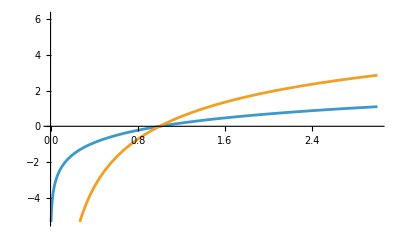

```mathematica
Plot[{Log[x],logApproximation[3,3][x]},{x,0,3}]
```

#### relaxedRelativeEntropy

Implements the Relative Entropy for matrices using the relaxation illustrated above.  where A and B are PSD matrices and the fractional power denotes the principal square root of the matrix and the equivalent negative power the principal square root of the matrix's inverse. The function  is implemented to act on the eigenvalues of the functions.

```mathematica
relaxedRelativeEntropy[m_,k_,A_,B_]:=-MatrixPower[A,1/2].MatrixFunction[logApproximation[m,k],MatrixPower[A,-1/2].B.MatrixPower[A,-1/2]].MatrixPower[A,1/2]
```

```mathematica
makeSymbolicMatrix[name_,size_,symmetry_:"symmetric"]:=If[symmetry=="symmetric",Table[If[i<=j,ToExpression[name][i,j],ToExpression[name][j,i]],{i,1,size},{j,1,size}],Table[If[i<j,ToExpression[name][i,j],If[i==j,0,-ToExpression[name][j,i]]],{i,1,size},{j,1,size}]]
```

#### kmsConstraints

Potentially Deprecated

```mathematica
kmsConstraints[m_,k_,A_,B_,C_]:=Module[
{(*Get the size of the input matrices*)
n=Length[A],
(*Define the ZX,ZY and TX,TY matrices symbolically such that Z=ZX+i*ZY same for T. *)
zXMatrices,
tXMatrices,
zYMatrices,
tYMatrices,
(*Get the abscissas and weights*)
abscissas=Join[{0},(#+1)/2&/@abscissas[m]],weights=Join[{1/m^2},getWeights[m]],
(*Define other variables*)
equalityConditions,zConditions,tConditions,constraints,variables
},
zXMatrices=Table[If[i==1,B,makeSymbolicMatrix[ToExpression["ZX"<>ToString[i-1]],n,"symmetric"]],{i,1,k+1}];
tXMatrices=Table[makeSymbolicMatrix[ToExpression["TX"<>ToString[j]],n,"symmetric"],{j,1,m}];
zYMatrices=Table[If[i==1,0,makeSymbolicMatrix[ToExpression["ZY"<>ToString[i-1]],n,"antisymmetric"]],{i,1,k+1}];
tYMatrices=Table[makeSymbolicMatrix[ToExpression["TY"<>ToString[j]],n,"antisymmetric"],{j,1,m}];
(*Get the equality condition for the T matrices*)
equalityConditions=Sum[weights[[i]]*(tXMatrices[[i]]+I*tYMatrices[[i]]),{i,1,m}]==-2^(-k)*C;

(*Get the block matrix conditions for the Z and T matrices*)
zConditions=Table[ {{zXMatrices[[i]],zXMatrices[[i+1]]},{zXMatrices[[i+1]],A}}+I*{{zYMatrices[[i]],zYMatrices[[i+1]]},{zYMatrices[[i+1]],0}}\[VectorGreaterEqual]0
,{i,1,k}];
tConditions=Table[
{{zXMatrices[[k+1]]-A-tXMatrices[[j]],-Sqrt[abscissas[[j]]]*tXMatrices[[j]]},{-Sqrt[abscissas[[j]]]*tXMatrices[[j]],A-abscissas[[j]]*tXMatrices[[j]]}} +I*{{zYMatrices[[k+1]]-tYMatrices[[j]],-Sqrt[abscissas[[j]]]*tYMatrices[[j]]},{-Sqrt[abscissas[[j]]]*tYMatrices[[j]],-abscissas[[j]]*tYMatrices[[j]]}}\[VectorGreaterEqual]0
,{j,1,m}];

(*Compress contraints into a singular one*)
constraints=And@@Join[zConditions,tConditions]&&equalityConditions;

(*Append the domains to the matrices, excluding Z0 which is fully defined*)
variables=DeleteCases[#∈Reals &/@DeleteDuplicates[Flatten[Join[zYMatrices,Rest[zXMatrices],tXMatrices,tYMatrices]],#1==-#2||#1==#2&],True];


(*Return*)
{variables,tConditions,zConditions,equalityConditions,zXMatrices,zYMatrices,tXMatrices,tYMatrices}
]
```

## Implementation

### Anharmonic Oscillator

```mathematica
L=6;
m=3;
k=3;

operatorLetters={x,p};

H:=p**p+x**x**x**x;

BcalLby2=generateOperatorSet[L/2,operatorLetters];
BcalLminus2=generateOperatorSet[L-2,operatorLetters];
BcalLby2minus2=generateOperatorSet[L/2-2,operatorLetters];
```

Produce and Solve the Schwinger Dyson Relations

```mathematica
schwingerDysonRelations=produceSwingerDyson[BcalLminus2,H];
```

```mathematica
{schwingerDysonReplacementRule,independentVariables}=solveRelations[schwingerDysonRelations];
```

Set up the Matrices  using the solved S-D relations

```mathematica
MofL=generateODaggerOMatrix[BcalLby2]/.schwingerDysonReplacementRule;
```

```mathematica
CofL=generateODaggerCommutatorHOMatrix[BcalLby2minus2,H]/.schwingerDysonReplacementRule;
```

```mathematica
AofL=generateODaggerOMatrix[BcalLby2minus2]/.schwingerDysonReplacementRule;
```

```mathematica
BofL=generateOODaggerMatrix[BcalLby2minus2]/.schwingerDysonReplacementRule;
```

Get the coefficients of the matrices

```mathematica
dictM= returnCoefficients[MofL];
dictA=returnCoefficients[AofL];
dictB=returnCoefficients[BofL];
dictC=returnCoefficients[CofL];
```

Define the SearchSpace parameters and constraints

```mathematica
EcalL=finalSearchSpace[MofL,independentVariables];
```

```mathematica
domainedEcalL=asignDomains[EcalL];
```

Export Parameters and Matrices as a json file.

```mathematica
Export["/home/pripoll/Documents/Uni_Classes/Masters_thesis/anharmonic_thermal/thermal_anharmonic/wolfram_output/anharmonic_output_for_l="<>ToString[L]<>"_m="<>ToString[m]<>"_k="<>ToString
[k]<> ".json",<|
"parameters"-><|
"type"->"Anharmonic",
"L"->L,
"quadrature"->getQuadrature[m],
"n"->Length[BcalLby2minus2],
"k"->k
|>,
"domains"->domainedEcalL,
"M"->dictM,
"A"-> dictA,
"C"-> dictC,
"B"-> dictB
|>]
```

/home/pripoll/Documents/Uni_Classes/Masters_thesis/anharmonic_thermal/thermal_anharmonic/wolfram_output/anharmonic_output_for_l=6_m=3_k=3.json

### Harmonic Oscillator

```mathematica
Lharmonic=12;
mharmonic=4;
kharmonic=4;

operatorLettersHarmonic= {x,p};

Hharmonic=p**p*1/2+x**x*1/2;

BcalLby2Harmonic=generateOperatorSet[Lharmonic/2,operatorLettersHarmonic];
BcalLminus2Harmonic=generateOperatorSet[Lharmonic-2,operatorLettersHarmonic];
BcalLby2minus2Harmonic=generateOperatorSet[Lharmonic/2-2,operatorLettersHarmonic];
```

Produce and Solve the Schwinger Dyson Relations

```mathematica
schwingerDysonRelationsHarmonic=produceSwingerDyson[BcalLminus2Harmonic,Hharmonic];
```

```mathematica
{schwingerDysonReplacementRuleHarmonic,independentVariablesHarmonic}=solveRelations[schwingerDysonRelationsHarmonic];
```

Set up the Matrices  using the solved S-D relations

```mathematica
MofLHarmonic=generateODaggerOMatrix[BcalLby2Harmonic]/.schwingerDysonReplacementRuleHarmonic;
```

```mathematica
CofLHarmonic=generateODaggerCommutatorHOMatrix[BcalLby2minus2Harmonic,Hharmonic]/.schwingerDysonReplacementRuleHarmonic;
```

```mathematica
AofLHarmonic=generateODaggerOMatrix[BcalLby2minus2Harmonic]/.schwingerDysonReplacementRuleHarmonic;
```

```mathematica
BofLHarmonic=generateOODaggerMatrix[BcalLby2minus2Harmonic]/.schwingerDysonReplacementRuleHarmonic;
```

Get the coefficients of the matrices

```mathematica
dictMHarmonic= returnCoefficients[MofLHarmonic];
dictAHarmonic=returnCoefficients[AofLHarmonic];
dictBHarmonic=returnCoefficients[BofLHarmonic];
dictCHarmonic=returnCoefficients[CofLHarmonic];
```

Define the SearchSpace parameters and constraints

```mathematica
EcalLHarmonic=finalSearchSpace[MofLHarmonic,independentVariablesHarmonic];
```

```mathematica
domainedEcalLHarmonic=asignDomains[EcalLHarmonic];
```

Export Parameters and Matrices as a json file.

```mathematica
Export["/home/pripoll/Documents/Uni_Classes/Masters_thesis/anharmonic_thermal/thermal_anharmonic/wolfram_output/harmonic_output_for_l="<>ToString[Lharmonic]<>"_m="<>ToString[mharmonic]<>"_k="<>ToString
[kharmonic]<> ".json",<|
"parameters"-><|
"type"->"Harmonic",
"L"->Lharmonic,
"quadrature"->getQuadrature[m],
"n"->Length[BcalLby2minus2Harmonic],
"k"->kharmonic
|>,
"domains"->domainedEcalLHarmonic,
"M"->dictMHarmonic,
"A"-> dictAHarmonic,
"C"-> dictCHarmonic,
"B"-> dictBHarmonic
|>]
```

/home/pripoll/Documents/Uni_Classes/Masters_thesis/anharmonic_thermal/thermal_anharmonic/wolfram_output/harmonic_output_for_l=12_m=4_k=4.json

```mathematica
Length[BcalLby2minus2Harmonic]
```

31

```mathematica
BcalLby2minus2Harmonic
```

{1,x,p,x^2,x**p,p**x,p^2,x^3,x^2**p,x**p**x,x**p^2,p**x^2,p**x**p,p^2**x,p^3,x^4,x^3**p,x^2**p**x,x^2**p^2,x**p**x^2,x**p**x**p,x**p^2**x,x**p^3,p**x^3,p**x^2**p,p**x**p**x,p**x**p^2,p^2**x^2,p^2**x**p,p^3**x,p^4}

```mathematica
MofLHarmonic//MatrixForm
```

### Next Up

Thus far, the Hankel matrix should be working and the solve expression thing as well. Roadmap:

	>Clean Up the Code. Make sure everything works fine afterwards DONE
	
	>Make a function that assigns the independent variables domains DONE
	
	>Check that the SDP runs with what you have (it probably wont get anything back. This is a cause of concern to be addressed but for now just check that you can run the non explicitly Hermitian 		matrix SDP) DONE
	
	>Make functions to make the A B and C matrices DONE
	
	>Pivot point for next big goal: Look into the logarithm approximation. DONE
	
	>The logarithm approximation does not seem to work as intended. That is something to be looked into
	
	>Proof of concept for how to implement the entirety of the positivity constraints as one matrix seems to work. Make it more robust. This could also be a good way to pass it to the sdp-gmp thing if 	needed (IF I ever figure out how to do Hermitian sdp with that). Mathematica only works well (from what I can tell for now) with fully symmetric matrices. NOPE
	
	>Run the SDP (it will probably not work) and then talk about the code. Moreover, there is a chance that the code never finds suitable points. If this persists after making the SDP run consistently in 	the full form then look into:
		~Not using the ordering (p always to the right) in the NC rules but instead let the canonical relations take care of that.
			→Nope this is not it either. Although there seems to be an issue with the replacement rules and the ordering, the canonical relations are equivalent to the ordering.
		~Check wether the independent variables are chosen erroneously.
			 → This shouldn't matter. I should be able to choose any independent variables I want.
		~Try using a search-space for a few variables.
			→Doesn't seem to yield anything.
		~Look at other bootstrap papers to see if they have more details in this cases.
		!Don't forget to illustrate all of this points properly so that during presentation of the code you can point to this approaches for completeness.
		
		→After running a hand built example for the sdp and getting no points again I have noticed that this happens when I add the T matrix constraints. No longer true after fixing the commutation 			replacement rules.
		
		~After fixing the bug with the handling of the commutators, I can't get points even when I have only the M matrix. I need to look into why that is.
		→I will write the function